| Estimate | Standard Error | t-Statistic | P-Value
1 | 199.855 | 12.2341 | 16.3359 | 3.35037×10^-6
x | -63.7083 | 4.02718 | -15.8196 | 4.04683×10^-6

{q→200,Δq→12}

0.09

{{dc→4.5,dc→-87.11},Δdc→0.09}

{{dac→13.2,dac→18.4},Δdac→0.7}

{Φ→0.171,ΔΦ→0.0133}

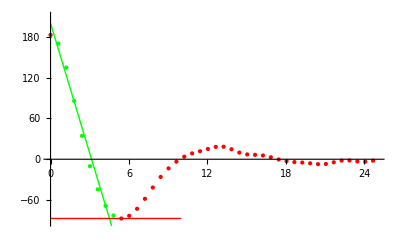

```mathematica
(*Import Data from files*)
Clear[lFit, Q, Φ, ρ];
prefix = "PET-";
sample = "200";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".cor","Table"];


(*Split Data into parts for linear fit and for the rest*)
sampleSize = 8;
linearData =  Take[rawData, {2,sampleSize}];
afterLinearData =  Take[rawData, -(Length[rawData ] - sampleSize)];
nonLinearData = Join[Take[rawData, 1], afterLinearData];

(*Find Min and Max of data, also find 2nd local max*)
minMax = {First@SortBy[rawData,Last], Last@SortBy[rawData,Last]};
localMax = Last@SortBy[afterLinearData,Last];

(*Linear fit*)
lFit = LinearModelFit[linearData,x,x];
lFit["ParameterTable"]


(*Relevant points*)


Δq = lFit["ParameterTable"][[1]][[1]][[2]][[3]];
q = {"q"-> Round[lFit["Function"][0]], "Δq"->Round[Δq]}
Δm = lFit["ParameterTable"][[1]][[1]][[3]][[3]];
dcP = Solve[lFit["BestFit"]+Δq-Δm*x== minMax[[1]][[2]], x][[All, 1, 2]][[1]];
dcT = {Solve[lFit["BestFit"] == minMax[[1]][[2]], x][[All, 1, 2]][[1]], minMax[[1]][[2]]};
Δdc = Round[dcT[[1]] - dcP,0.01]
dc = {"dc"->Round[#, 0.01]&/@dcT, "Δdc"->Round[Δdc, 0.01]}
dac = {"dac"->Round[#, 0.1]&/@localMax, "Δdac"-> Round[localMax[[1]]*0.05, 0.1]}

ρ= 37.56;
Phi = Round[Solve[lFit["Function"][0]== Φ(1-Φ)*ρ^2,Φ][[All, 1, 2]][[1]],0.001];
ΔPhi = Round[Solve[lFit["Function"][0] + Δq== Φ(1-Φ)*ρ^2,Φ][[All, 1, 2]][[1]] - Phi, 0.0001];
{"Φ"->Phi,"ΔΦ"->ΔPhi}


Export[path<>"-Q-Dc-Dac-Dacy.txt", {q, dc, dac, {"Φ"->Phi,"ΔΦ"->ΔPhi}}, "Table"];
Export[path <> ".cor.txt", lFit["BestFit"], "String"];

(*Plot functions and data*)
Show[ListPlot[nonLinearData,PlotStyle->Red], ListPlot[linearData,PlotStyle->Green], Plot[{lFit["BestFit"]},{x,0,8}, PlotStyle-> Green], Plot[{minMax[[1]][[2]]},{x,0,10}, PlotStyle-> Red], PlotRange-> {{0,25},{minMax[[1]][[2]] - 5,lFit["Function"][0]+ 10}}]
```